Quantum-stochasticity-induced asymmetry in the angular distribution of electrons in a quasiclassical regime

Paper: Hu et al, Phys Rev A 102, 042218 (2020)
Notebook: Óscar Amaro, February 2023 @ GoLP-EPP

Introduction
Quantum stochastic angular broadening in electron-LP laser scattering.
We compare this notebook’s implementation with data retrieved from the paper (with WebPlotDigitizer).

## Figures 4, 5 and 6

FIG. 4

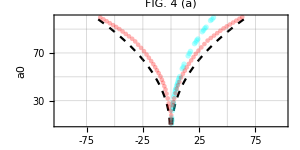

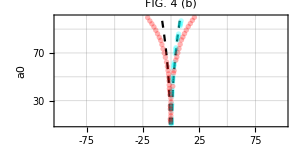

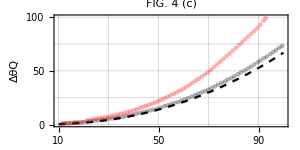

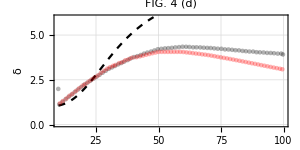

FIG. 5

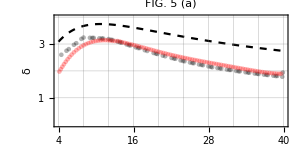

FIG. 6

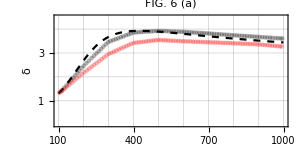

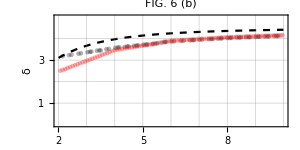

```mathematica
SetDirectory[NotebookDirectory[]];
Clear[Δθy,Δθx,Δθi,Δθp,ϵ0,γ,m,τ,T0,σy,W0,a0,δ,ΔθQ,imgsz,asp,fig4alst,fig4alst2,fig4blst,fig4blst2]
asp=1/2;imgsz=300;

(* fixed parameters, beginning of section IV *)
γ=ϵ0/0.511;
Δθi=0.001; (*[rad]*)
T0=1;
(* ϵ0=300 MeV, W0=3 μm, τ=8 T0, σy=0.3 μm *)

(* equations *)
Δθy=Sqrt[(Δθi)^2+(Δθp)^2];(*14*)
Δθp=(1.07a0^2 σy τ)/(γ^2 W0^2 T0);(*15*)
(*ΔθQ =(2Sqrt[2Log[2]σpx])/(m γ);(*16*)*)
ΔθQ=(3.3 10^-6 )(a0^2.26) (γ^-0.24) (τ/T0)^0.5;(*17*)
Δθx=Sqrt[ΔθQ^2+Δθy^2];(* 19 *)
δ=Δθx/Δθy//Simplify;(*Sqrt[1+ΔθQ^2/((Δθi)^2+(Δθp)^2)]*)

Print["FIG. 4"]
(*Fig4 a*)
fig4alst=Table[{(1000 Δθx/.{ϵ0->300,W0->3,τ->8,σy->0.3}),a0},{a0,10,100,1}];
fig4alst2=Table[{-(1000 Δθx/.{ϵ0->300,W0->3,τ->8,σy->0.3}),a0},{a0,10,100,1}];
Show[{ListPlot[{fig4alst,fig4alst2},Joined->True,PlotRange->{{-100,+100},{10,100}},Frame->True,FrameLabel->{"θx","a0"},FrameTicks->{{{30,50,70,90},None},{{-75,-50,-25,0,25,50,75},None}},GridLines->{{-75,-50,-25,0,25,50,75},{30,50,70,90}},ImageSize->imgsz, AspectRatio->asp,PlotStyle->{{Black,Dashed}},PlotLabel->"FIG. 4 (a)"],ListPlot[Import["data/fig4a_estimate.csv"],PlotStyle->{Cyan,Opacity[0.3]},PlotLegends->"Cyan Estimate"],ListPlot[Import["data/fig4a_numerical.csv"],PlotStyle->{Red,Opacity[0.3]},PlotLegends->"Red Numerical"]}]

(*Fig4 b*)
fig4blst=Table[{(1000 Δθy/.{ϵ0->300,W0->3,τ->8,σy->0.3}),a0},{a0,10,100,1}];
fig4blst2=Table[{-(1000 Δθy/.{ϵ0->300,W0->3,τ->8,σy->0.3}),a0},{a0,10,100,1}];
Show[{ListPlot[{fig4blst,fig4blst2},Joined->True,PlotRange->{{-100,+100},{10,100}},Frame->True,FrameLabel->{"θy","a0"},FrameTicks->{{{30,50,70,90},None},{{-75,-50,-25,0,25,50,75},None}},GridLines->{{-75,-50,-25,0,25,50,75},{30,50,70,90}},ImageSize->imgsz, AspectRatio->asp,PlotStyle->{{Black,Dashed}},PlotLabel->"FIG. 4 (b)"],ListPlot[Import["data/fig4b_estimate.csv"],PlotStyle->{Cyan,Opacity[0.3]},PlotLegends->"Cyan Estimate"],ListPlot[Import["data/fig4b_numerical.csv"],PlotStyle->{Red,Opacity[0.3]},PlotLegends->"Red Numerical"]}]

(*Fig4 c*)
Show[{Plot[(1000 ΔθQ/.{ϵ0->300,W0->3,τ->8,σy->0.3}),{a0,10,100},PlotRange->{{10,100},{0,100}},Frame->True,FrameLabel->{"a0","ΔθQ"},FrameTicks->{{{0,25,50,75,100},None},{{10,30,50,70,90},None}},GridLines->{{10,30,50,70,90},{0,25,50,75,100}},ImageSize->imgsz, AspectRatio->asp,PlotStyle->{{Black,Dashed}},PlotLabel->"FIG. 4 (c)"],
ListPlot[Import["data/fig4c_estimate.csv"],PlotStyle->{Black,Opacity[0.3]},PlotLegends->"Black Estimate"],ListPlot[Import["data/fig4c_numerical.csv"],PlotStyle->{Red,Opacity[0.3]},PlotLegends->"Red Numerical"]}]

(*Fig4 d*)
Show[{Plot[(δ/.{ϵ0->300,W0->3,τ->8,σy->0.3}),{a0,10,100},PlotRange->{{10,100},{0,6}},GridLines->Automatic,Frame->True,FrameLabel->{"a0","δ"},ImageSize->imgsz, AspectRatio->asp,PlotStyle->{{Black,Dashed}},PlotLabel->"FIG. 4 (d)"],
ListPlot[Import["data/fig4d_estimate.csv"],PlotStyle->{Black,Opacity[0.3]},PlotLegends->"Black Estimate"],ListPlot[Import["data/fig4d_numerical.csv"],PlotStyle->{Red,Opacity[0.3]},PlotLegends->"Red Numerical"]}]

Print["FIG. 5"]
(*Fig5 a*)
Show[{Plot[(δ/.{a0->30,ϵ0->300,W0->3,σy->0.3}),{τ,4,40},PlotRange->{{4,40},{0,4}},Frame->True,FrameLabel->{"τ/T0","δ"},FrameTicks->{{{1,2,3,4},None},{Table[x,{x,4,41,4}],None}},GridLines->{Table[x,{x,4,41,4}],{1,2,3,4}},ImageSize->imgsz, AspectRatio->asp,PlotStyle->{{Black,Dashed}},PlotLabel->"FIG. 5 (a)"],ListPlot[Import["data/fig5a_estimate.csv"],PlotStyle->{Black,Opacity[0.3]},PlotLegends->"Black Estimate"],ListPlot[Import["data/fig5a_MCM.csv"],PlotStyle->{Red,Opacity[0.3]},PlotLegends->"Red MCM"]}]

Print["FIG. 6"]
(*Fig6 a*)
Show[{Plot[(δ/.{a0->30,W0->3,τ->8,σy->0.3}),{ϵ0,100,1000},PlotRange->{{100,1000},{0,4.5}},Frame->True,FrameLabel->{"ϵ0[MeV]","δ"},FrameTicks->{{{1,2,3,4},None},{Table[x,{x,100,1001,100}],None}},GridLines->{Table[x,{x,100,1001,100}],{1,2,3,4}},ImageSize->imgsz, AspectRatio->asp,PlotStyle->{{Black,Dashed}},PlotLabel->"FIG. 6 (a)"],ListPlot[Import["data/fig6a_estimate.csv"],PlotStyle->{Black,Opacity[0.3]},PlotLegends->"Black Estimate"],ListPlot[Import["data/fig6a_MCM.csv"],PlotStyle->{Red,Opacity[0.3]},PlotLegends->"Red MCM"]}]

(*Fig6 b*)
Show[{Plot[(δ/.{a0->30,ϵ0->300,τ->8,σy->0.1W0}),{W0,2,10},PlotRange->{{2,10},{0,5}},Frame->True,FrameLabel->{"W0[μm]","δ"},FrameTicks->{{{1,2,3,4},None},{Table[x,{x,2,11,1}],None}},GridLines->{Table[x,{x,2,11,1}],{1,2,3,4}},ImageSize->imgsz, AspectRatio->asp,PlotStyle->{{Black,Dashed}},PlotLabel->"FIG. 6 (b)"],ListPlot[Import["data/fig6b_estimate.csv"],PlotStyle->{Black,Opacity[0.3]},PlotLegends->"Black Estimate"],ListPlot[Import["data/fig6b_MCM.csv"],PlotStyle->{Red,Opacity[0.3]},PlotLegends->"Red MCM"]}]
```